```mathematica
(*This is the path that contains the executables and loads SDPB*)
executablesPath = "/home/pano/.local/src/sdpb/build";
<<"/home/pano/.local/src/sdpb/mathematica/SDPB.m";
```

# Gap Consistency Checks

## We constrain possible values for the Gap of a CFT by searching for a functional which breaks everything hehe.

## Defining the Matrix Problem

Let’s first construct the matrix problem and tell SDPB to export the description into a JSON file for SDPB to actually run the thing.

terminateReason = "found dual feasible solution";
primalObjective = 729915519003701.5714089039221496311588839863299615692521801521245117246499083375901817152542432467236168538624426443711680088432390707006718590361431883243850447820029672634546825007052112508941591978991792338093977742760816397064312971898423895622815162030826720500598279671716224681282421046665348421542330633;
dualObjective   = 9.787234009819478113938937707531029622429862955417123001213801066886456706843792070544539866940793408340425391080638539601512524374576324402616936188630968270779565528463162502176376653269146408264096648110261523455172740193731365425909297474831628503908572315043399586916491432552166354222578623958159953668928e-21;
dualityGap      = 0.9999999999999999999999999999999999731825567342955896973802512863930025346752078266555270073758066282562006625096317660834428517258641616454047802716507492284467709103569658603668419276786733643457515015367633759758794606148675738757956123981045266937250405178981406372413165814549880163551411070472291565706969;
primalError     = 3.467792046403115823415106691577592954920811725397777287451020959286229117455651393448219609893653858124043104450246408126236728058437299887832425171162832491847683003618460014286779568498522583280602718831662130044742323420690371636824799417720517161710173897094158923997351787592367232274642391733941513542025e-197;
dualError       = 8.509696725116341472928276148792678071545467608690244061050895143178552591592856751962270281418793730792837661415921817559403771035102146210202028585691995686193602921781366454804567689189723581385651640901915793552399939593373691571576575909694930848281216883897077381515552678139096450575895867386110346687933e-261;
Solver runtime  = 13;

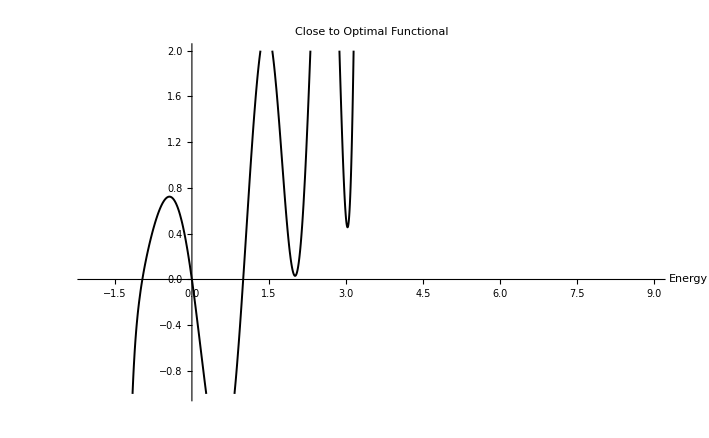

```mathematica
(*Precision and directories*)
precision = 1024;
file ="/home/pano/projects/sdpb-test/pmp.json";
sdpdir="/home/pano/projects/sdpb-test/sdp";
outdir="/home/pano/projects/sdpb-test/out";
outfile ="/home/pano/projects/sdpb-test/out/y.txt";
Run[StringRiffle[{
"rm -rf",
FileNameJoin[{sdpdir,"*"}],
sdpdir<>".ck",
FileNameJoin[{outdir,"*"}]
}]];

(*Maximum order of derivatives in the linear functional a*)
P=45; 

(*Central charge*)
c = 12; 

(*Gap energy*)
E0=1; 

(*Threshold*)
threshold=10^-20; 

(*Polynomial generator function*)
poly[n_,E0_,x_]:=Sum[StirlingS2[n,k](-2π (x+E0))^k,{k,1,n}]; 

(*Construct a module that does this whole sdpb definition thingy*)
solve[gapEnergy_:E0,centralCharge_:c, order_:P, precision_:precision,thresh_:threshold]:=
Module[{
E0=gapEnergy,
c=centralCharge,
NN=Floor[order/2],
threshold=thresh,
objective,
normalization,
matrices
},

(*Objective vector*)
(*objective = {0}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN]);*)
(*objective = (poly[2#+1,0,-c/12]&/@Range[0,NN]);*)
objective = {0}~Join~(-(poly[2#+1,0,-c/12]&/@Range[0,NN]));

(*Normalization vector*)
(*normalization = {1}~Join~(Range[0,NN]*0);*)
(*normalization = (poly[2#+1,E0,0.5]&/@Range[0,NN]);*)
normalization = {1}~Join~(Range[0,NN]*0);

(*Polynomial list*)
matrices={
PositiveMatrixWithPrefactor[<|
(*"polynomials"->{{{0}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
(*"polynomials"->{{(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
"polynomials"->{{{0}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}
|>],
PositiveMatrixWithPrefactor[<|
"prefactor"-> 1,
"polynomials"->{{{threshold}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN])}}
|>]
};

(*Define SDP*)
WritePmpJson[file, SDP[objective,normalization,matrices], precision];

(*Run the magical code to solve*)
Run[StringRiffle[{
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[precision], file, sdpdir
}]];
Run[StringRiffle[{
"mpirun"
,FileNameJoin[{executablesPath,"sdpb"}]
,"-s", sdpdir, "-o", outdir
,"--precision="<> ToString[precision]
,"--noFinalCheckpoint"
,"--maxIterations="<>ToString[5000]
,"--dualityGapThreshold=1e-30"
, "--writeSolution=\"x,y,z\""
,"--maxComplementarity=1e+100"
,"--findDualFeasible"
}]];
(*ToExpression@Import[FileNameJoin[{outdir,"out.txt"}],"Text"];*)
fullResult = Import[FileNameJoin[{outdir,"out.txt"}], "String"];
Echo[fullResult];
];
solve[]
(* Get the optimal vector *)
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Plot[α/threshold/10,{x,-c/12-E0,9},PlotRange->{-1,2} ,MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

-9.78723×10^-21

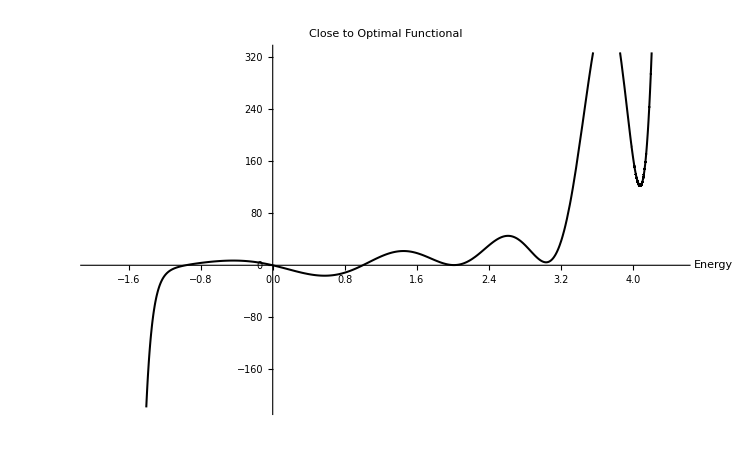

```mathematica
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Echo[(α/.x->(-1))//N];
Plot[α/threshold,{x,-c/12-E0,4.5},MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

```mathematica
(α/.x->(-1))
```

-9.9999999999850799779390888398753732149340492500125376305015566090340266685713218845609710325723995072375847844725178751100828040997272175691606680431230730650163853521765658120162805612621258348408691687117528526808865304737902665703244479149105501636218224173678052771034890952889214281076595754262702×10^-21

```mathematica
StringRiffle[{
"rm -rf",
FileNameJoin[{sdpdir,"*"}],
sdpdir<>".ck",
FileNameJoin[{outdir,"*"}],
"&&",
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[precision], file, sdpdir,
 "&&",
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision="<> ToString[precision],
"--noFinalCheckpoint"
,"--maxIterations="<>ToString[5000]
,"--dualityGapThreshold=1e-10"
, "--writeSolution=\"x,y,z\""
}]//CopyToClipboard
```